Wolfram Online Mini Campus. Part 2

Instagram Posts
Pinterest Posts
"Translation" of SageMath Online Mini Campus. Part 2

Series

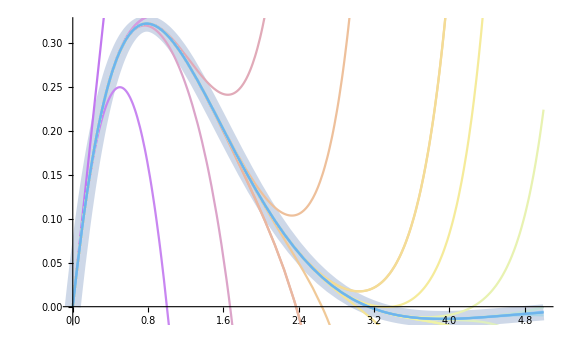

```mathematica
p1=Plot[Sin[z]Exp[-z],{z, 0,5},PlotStyle->{Thickness[0.02],Opacity[0.3]}];
p2=Plot[Evaluate[Table[Normal[Series[Sin[z]Exp[-z],{z, 0,n}]],{n,1,24}]],{z, 0,5},PlotStyle->"Pastel"];
Show[p1,p2,ImageSize->Large]
```

```mathematica
Series[Sin[z]Exp[-z],{z,0,5}]
Normal[Series[Sin[z]Exp[-z],{z,0,5}]]
```

z-z^2+z^3/3-z^5/30+O[z]^6

z-z^2+z^3/3-z^5/30

SuperFunctions: LearnDistribution

```mathematica
boston=ResourceData["Sample Data: Boston Homes"]; LDB=LearnDistribution[boston[All,{"RM","MEDV"}]]
```

LearnedDistribution[…]

```mathematica
syntheticboston=Table[SynthesizeMissingValues[LDB,{n,Missing[]}],{n,Range[4,8,0.2]}]
```

{RM→4.,MEDV→13.8998,RM→4.2,MEDV→12.1383,RM→4.4,MEDV→15.896,RM→4.6,MEDV→14.7524,RM→4.8,MEDV→15.7439,RM→5.,MEDV→16.1493,RM→5.2,MEDV→8.66548,RM→5.4,MEDV→15.8661,RM→5.6,MEDV→6.4613,RM→5.8,MEDV→19.673,RM→6.,MEDV→8.02271,RM→6.2,MEDV→11.3101,RM→6.4,MEDV→17.6313,RM→6.6,MEDV→23.5291,RM→6.8,MEDV→23.4427,RM→7.,MEDV→8.72414,RM→7.2,MEDV→33.9877,RM→7.4,MEDV→34.3501,RM→7.6,MEDV→30.8109,RM→7.8,MEDV→49.4371,RM→8.,MEDV→49.7051}

```mathematica
p1=ListPlot[boston[All,{"RM","MEDV"}],PlotLegends -> {"Data"}]; 
p2=ListPlot[syntheticboston,PlotStyle->Red,PlotLegends -> {"Synthetic Data"}];
Show[p1,p2,GridLines->Automatic,ImageSize->Large]
```

-Graphics-

Interactive Parameters

```mathematica
Manipulate[Show[ParametricPlot[{(Cos[a*t]^n+Sin[b*t]^m+1/c)*Sin[t],(Cos[a*t]^n+Sin[b*t]^m+1/c)*Cos[t]},{t,0,2π}],
                                 Plot[Cos[a*t]^n+Sin[b*t]^m+1/c,{t,0,2π},PlotStyle->Dashed],
             PlotRange->{{-2.2,2.2},{-2.2,2.2}},ImageSize->Large],
                        {a,Range[2,4,1]},{b,Range[4,8,1]},{c,Range[4,8,1]},{n,Range[2,8,1]},{m,Range[2,8,1]}]
```

3D Graphics Objects

```mathematica
Manipulate[Graphics3D[{Hue[n],EdgeForm[{Gray,Thickness[0.01]}],Opacity[.5],PolyhedronData[p,"GraphicsComplex"]},
                                                 Boxed->False,ImageSize->Large],
                       {p,PolyhedronData["Archimedean"]},{n,Range[0.1,0.9,0.1]}]
```

```mathematica
Show[PolyhedronData["GreatRhombicosidodecahedron"] /.
        Polygon[p_]:> MapIndexed[{Glow[Hue[Mod[First[#2],64]/64]],Black,Opacity[0.8],Polygon[#1]} &,p],
    Boxed->False,ImageSize->Large]
```

-Graphics3D-

Contour PLots

```mathematica
ContourPlot[{x1^2+x1*x2+x2^2+2*x1+6*x2+3==0,x1^2+x1*x2-x2^2+2*x1+6*x2+3==0,
                          x1^2-x1*x2+x2^2+2*x1+6*x2+3==0,-x1^2+x1*x2+x2^2+2*x1+6*x2+3==0},
                           {x1,-10,10},{x2,-10,10},ContourStyle->"Pastel",GridLines->Automatic,ImageSize->Large, PlotLegends->"Expressions"]
```

-Graphics-

HTML & JavaScript

```mathematica
EmbeddedHTML["<p id='js_output'/>
<script>var s='358***морозИсолнцеДЕНЬчудестный***123'; document.getElementById('js_output').innerHTML=s+' - '+s.length+' symbols';</script>"]
```

Null«162»<p id='js_output'/>
<script>var s='358***морозИсолнцеДЕНЬчудестный***123'; document.getElementById('js_output').innerHTML=s+' - '+s.length+' symbols';</script>

```mathematica
EmbeddedHTML["<style>@import url('https://fonts.googleapis.com/css?family=Sancreek|Monoton|Cabin Sketch&effect=3d|fire-animation');</style>
<p style='color:darkred; font-family:Sancreek; font-size:250%;' class='font-effect-3d'>&#x1F4D5; &nbsp; Choose your style!</p>
<p style='color:darkslategray; font-size:150%; font-family:Monoton; text-shadow:5px 5px 5px #bbb;'>&#x1F4D3;&nbsp; Choose &nbsp; your &nbsp; style!</p>                                                                           
<p style='color:steelblue; font-size:250%; font-family:Cabin Sketch;' class='font-effect-fire-animation'>&#x1F4D8; &nbsp; Choose your style!</p>"]
```

Null<style>@import url('https://fonts.go…x1F4D8; &nbsp; Choose your style!</p><style>@import url('https://fonts.googleapis.com/css?family=Sancreek|Monoton|Cabin Sketch&effect=3d|fire-animation');</style>
<p style='color:darkred; font-family:Sancreek; font-size:250%;' class='font-effect-3d'>&#x1F4D5; &nbsp; Choose your style!</p>
<p style='color:darkslategray; font-size:150%; font-family:Monoton; text-shadow:5px 5px 5px #bbb;'>&#x1F4D3;&nbsp; Choose &nbsp; your &nbsp; style!</p>                                                                           
<p style='color:steelblue; font-size:250%; font-family:Cabin Sketch;' class='font-effect-fire-animation'>&#x1F4D8; &nbsp; Choose your style!</p>

Services & Packages

```mathematica
$EmbeddableServices
```

{BingMaps,DeviantArt,EsriMap,GoogleDocs,GoogleForms,GoogleMaps,GoogleSheets,GoogleSlides,Imgur,Instagram,OpenStreetMap,Reddit,SoundCloud,Twitter,UStream,Vimeo,Vine,YouTube}

```mathematica
$Services
```

{ArXiv,BingSearch,ChemSpider,CrossRef,Dropbox,Facebook,Factual,FederalReserveEconomicData,Fitbit,Flickr,GoogleAnalytics,GoogleCalendar,GoogleContacts,GoogleCustomSearch,GooglePlus,GoogleTranslate,Instagram,LinkedIn,MailChimp,MicrosoftTranslator,Mixpanel,MusicBrainz,OpenLibrary,OpenPHACTS,PubChem,PubMed,Pushbullet,Reddit,RunKeeper,SeatGeek,SurveyMonkey,Twilio,Twitter,Wikipedia,Yelp}

```mathematica
$Packages
```

{DataDropClient`,ChannelFramework`,OAuthLoader`,OAuth`,EmbeddedService`,CalculateUtilities`AlgorithmUtilities`,CalculateUtilities`UserVariableUtilities`,CalculateScan`Packages`Get3DRange`,CalculateScan`Packages`Get2DRange`,CalculateScan`Packages`Get1DPolarPlotRange`,CalculateUtilities`SuggestPlotRanges`,MXNetLink`,NeuralNetworks`,DataResource`,ResourceSystemClient`,WebPredictions`,CloudSystem`Grammar`,CloudSystem`OutputSizeLimit`,CloudSystem`,IPOPTLink`,TypeSystem`,Macros`,Dataset`,CloudObject`,MUnit`,Parallel`Protected`,Parallel`Developer`,Parallel`Evaluate`,Parallel`Combine`,Parallel`Queue`Priority`,Parallel`Queue`FIFO`,Parallel`Queue`Interface`,Parallel`Concurrency`,Parallel`VirtualShared`,Parallel`Status`,SubKernels`LocalKernels`,Parallel`Palette`,Parallel`Parallel`,SubKernels`Protected`,SubKernels`,Parallel`Kernels`,Parallel`,Parallel`Preferences`,XMPTools`,CloudSystem`Preferences`,GraphicsTools`Wrappers`Tooltip`,GraphicsTools`Wrappers`TagBox`,GraphicsTools`Wrappers`Style`,GraphicsTools`Wrappers`EventHandler`,GraphicsTools`Wrappers`DynamicModule`,GraphicsTools`Wrappers`Dynamic`,GraphicsTools`Directives`Thickness`,GraphicsTools`Directives`Texture`,GraphicsTools`Directives`PointSize`,GraphicsTools`Directives`JoinForm`,GraphicsTools`Directives`FaceForm`,GraphicsTools`Directives`EdgeForm`,GraphicsTools`Directives`Directive`,GraphicsTools`Directives`Dashing`,GraphicsTools`Directives`Color`,GraphicsTools`Directives`CapForm`,GraphicsTools`Directives`Arrowheads`,GraphicsTools`Primitives`TetrahedronBox`,GraphicsTools`Primitives`PyramidBox`,GraphicsTools`Primitives`PrismBox`,GraphicsTools`Primitives`Inset3DBox`,GraphicsTools`Primitives`HexahedronBox`,GraphicsTools`Primitives`ConicHullRegion3DBox`,GraphicsTools`Primitives`InterpretationBox`,GraphicsTools`Primitives`TubeBox`,GraphicsTools`Primitives`Text3DBox`,GraphicsTools`Primitives`SphereBox`,GraphicsTools`Primitives`Raster3DBox`,GraphicsTools`Primitives`Polygon3DBox`,GraphicsTools`Primitives`Point3DBox`,GraphicsTools`Primitives`Line3DBox`,GraphicsTools`Primitives`GraphicsGroup3DBox`,GraphicsTools`Primitives`GraphicsComplex3DBox`,GraphicsTools`Primitives`Graphics3DBox`,GraphicsTools`Primitives`GeometricTransformation3DBox`,GraphicsTools`Primitives`CylinderBox`,GraphicsTools`Primitives`CuboidBox`,GraphicsTools`Primitives`ConeBox`,GraphicsTools`Primitives`BSplineSurface3DBox`,GraphicsTools`Primitives`BSplineCurve3DBox`,GraphicsTools`Primitives`BezierCurve3DBox`,GraphicsTools`Utilities`DirectivesUtils`,GraphicsTools`Utilities`OptionUtils`,GraphicsTools`Primitives`Arrow3DBox`,GraphicsTools`Utilities`ColorUtils`,GraphicsTools`Utilities`ObjectUtils`,GraphicsTools`Utilities`MessageUtils`,GraphicsTools`Utilities`DebugUtils`,GraphicsTools`Utilities`Utilities`,GraphicsTools`,CloudSystem`CloudGraphics3D`,CloudSystem`CloudGraphics`,Databases`,Databases`Entity`,Databases`Database`,Databases`SQL`,Databases`Schema`,DatabaseLink`,Databases`Python`,Databases`Common`,CompileAST`,CompileUtilities`,Compile`TypeSystem`Environment`FunctionDefinitionLookup`,Compile`TypeSystem`Environment`TypeEnvironment`,Compile`ResourceLoader`,Compile`TypeSystem`Bootstrap`Utilities`,Compile`TypeSystem`Bootstrap`ReinterpretCast`,Compile`TypeSystem`Bootstrap`Traits`,Compile`TypeSystem`Bootstrap`Float`,Compile`TypeSystem`Bootstrap`Unchecked`,Compile`TypeSystem`Bootstrap`TakeDrop`,Compile`TypeSystem`Bootstrap`Structural`,Compile`TypeSystem`Bootstrap`String`,Compile`TypeSystem`Bootstrap`Stream`,Compile`TypeSystem`Bootstrap`Random`,Compile`TypeSystem`Bootstrap`Parallel`,Compile`TypeSystem`Bootstrap`PackedArrayStructural2`,Compile`TypeSystem`Bootstrap`PackedArrayStructural`,Compile`TypeSystem`Bootstrap`PackedArrayPredicates`,Compile`TypeSystem`Bootstrap`PackedArrayMath`,Compile`TypeSystem`Bootstrap`PackedArray`,Compile`TypeSystem`Bootstrap`NumericArray`,Compile`TypeSystem`Bootstrap`Numeric`,Compile`TypeSystem`Bootstrap`MObject`,Compile`TypeSystem`Bootstrap`MinMax`,Compile`TypeSystem`Bootstrap`LibC`,Compile`TypeSystem`Bootstrap`InitializeRuntime`,Compile`TypeSystem`Bootstrap`Expression`,Compile`TypeSystem`Bootstrap`Debugging`,Compile`TypeSystem`Bootstrap`ClassSystem`,Compile`TypeSystem`Bootstrap`C`,Compile`TypeSystem`Bootstrap`Boolean`,Compile`TypeSystem`Bootstrap`Basics`,Compile`TypeSystem`Bootstrap`,Compile`TypeSystem`,Compile`Core`Debug`,SymbolicC`SymbolicCXX`,SymbolicC`Utilities`,SymbolicC`,Compile`Core`CodeGeneration`Backend`CXX`,Compile`Core`CodeGeneration`Backend`JSONSerializer`,Compile`Core`CodeGeneration`Backend`Interpreter`,Compile`Core`CodeGeneration`Backend`,Compile`Core`CodeGeneration`Passes`,Compile`Core`CodeGeneration`,Compile`Core`Optimization`NormalizeControlFlow`,Compile`Core`Optimization`OptimizeBasicBlocks`,Compile`Core`Optimization`RecordSetElement`,Compile`Core`Optimization`RecordFixedMTensor`,Compile`Core`Optimization`EmptyBlockRemoval`,Compile`Core`Optimization`SelectInstructionRemoval`,Compile`Core`Optimization`CommonSubexpressionElimination`,Compile`Core`Optimization`ExpressionNormalization`,Compile`Core`Optimization`FuseListMap`,Compile`Core`Optimization`SimplifyExpression`,Compile`Core`Optimization`,Compile`Core`Transform`ConstantUnfolding`,Compile`Core`Transform`Closure`,Compile`Core`Transform`,Compile`Core`PassManager`Identity`,Compile`Core`PassManager`,Compile`Core`Analysis`Properties`VariableValue`,Compile`Core`Analysis`Properties`BasicBlockLastPhi`,Compile`Core`Analysis`Properties`,Compile`Core`Analysis`Function`FunctionIsInlinable`,Compile`Core`Analysis`Properties`FunctionCallLinkage`,Compile`Core`Analysis`Function`FunctionInlineCost`,Compile`Core`Analysis`Function`,Compile`Core`Analysis`Loop`InductionVariable`,Compile`Core`Analysis`Loop`LoopInvariant`,Compile`Core`Analysis`Loop`LoopDetection`,Compile`Core`Analysis`Loop`,Compile`Core`Analysis`Utilities`ScalarExpression`,Compile`Core`Analysis`DataFlow`AvailableExpressions`,Compile`Core`Analysis`DataFlow`ReachingDefinition`,Compile`Core`Analysis`DataFlow`LiveInterval`,Compile`Core`Analysis`DataFlow`LiveVariablesAlternate`,Compile`Core`Analysis`Dominator`StrictPostDominator`,Compile`Core`Analysis`Dominator`PostDominator`,Compile`Core`Analysis`Dominator`ImmediatePostDominator`,Compile`Core`Analysis`Dominator`DominanceFrontier`,Compile`Core`Analysis`Dominator`,Compile`Core`Analysis`DataFlow`,Compile`Core`Analysis`Utilities`VariableList`,Compile`Core`Analysis`Utilities`SideEffecting`,Compile`Core`Analysis`Utilities`IntervalPartition`,Compile`Core`Analysis`Utilities`StronglyConnectedComponents`,Compile`Core`Analysis`Utilities`,Compile`Core`Analysis`,Compile`Core`Lint`Closure`,Compile`Core`Lint`,Compile`Core`IR`Internal`,Compile`Core`IR`Lower`Utilities`,Compile`TypeSystem`FunctionData`KernelFunction`,Compile`Core`IR`Lower`Utilities`LoweringTools`,Compile`Core`IR`Lower`TypePrediction`TypePrediction`,Compile`Core`IR`Lower`Primitives`Which`,Compile`Core`IR`Lower`Primitives`SetProperty`,Compile`Core`IR`Lower`Primitives`Continue`,Compile`Core`IR`Lower`Primitives`Break`,Compile`Core`IR`Lower`Primitives`SizeOf`,Compile`Core`IR`Lower`Primitives`Field`,Compile`Core`IR`Lower`Primitives`DeclareType`,Compile`Core`IR`Lower`Primitives`Structural`,Compile`Core`IR`Lower`Primitives`General`,Compile`Core`IR`Lower`Primitives`Typed`,Compile`Core`IR`Lower`Primitives`StackAllocate`,Compile`Core`IR`Lower`Primitives`Return`,Compile`Core`IR`Lower`Primitives`Inert`,Compile`Core`IR`Lower`Primitives`NDSolve`,Compile`Core`IR`Lower`Primitives`Function`,Compile`Core`IR`Lower`Primitives`Part`,Compile`Core`IR`Lower`Primitives`While`,Compile`Core`IR`Lower`Primitives`List`,Compile`Core`IR`Lower`Primitives`Error`,Compile`Core`IR`Lower`Primitives`If`,Compile`Core`IR`Lower`Primitives`FunctionVariable`,Compile`Core`IR`Lower`Primitives`Compound`,Compile`Core`IR`Lower`Primitives`Symbol`,Compile`Core`IR`Lower`Primitives`Module`,Compile`Core`IR`Lower`Primitives`Atom`,Compile`Core`IR`Lower`Primitives`Set`,Compile`Core`IR`Lower`Primitives`Operation`,Compile`Core`IR`Lower`Primitives`,Compile`Core`IR`Lower`Builder`,Compile`Core`IR`Lower`,Compile`Core`IR`TypeName`,Compile`Core`IR`GlobalValue`,Compile`Core`IR`Instruction`Utilities`InstructionMatch`,Compile`Core`IR`Instruction`Utilities`InstructionOperator`,Compile`Core`IR`Instruction`Utilities`,Compile`Core`IR`Instruction`NewRecordInstruction`,Compile`Core`IR`Instruction`GetFieldInstruction`,Compile`Core`IR`Instruction`SetFieldInstruction`,Compile`Core`IR`Instruction`RecordSelectInstruction`,Compile`Core`IR`Instruction`RecordRestrictInstruction`,Compile`Core`IR`Instruction`RecordExtendInstruction`,Compile`Core`IR`Instruction`SelectInstruction`,Compile`Core`IR`Instruction`UnaryInstruction`,Compile`Core`IR`Instruction`TypeCastInstruction`,Compile`Core`IR`Instruction`,Compile`Core`IR`,Compile`Core`Utilities`Visualization`Detail`LongestPath`,Compile`Core`Utilities`Visualization`Detail`,Compile`Core`Utilities`Visualization`,Compile`Core`Utilities`,Compile`Core`,Compile`API`FunctionCompile`,LLVMCompileTools`Finalize`,Compile`Core`Lint`Types`,Compile`Core`Lint`Utilities`,Compile`Core`Lint`IR`,Compile`Core`Transform`Closure`ResolveLambdaClosure`,Compile`Core`Transform`Closure`ResolveClosureVariableType`,Compile`Core`Analysis`Properties`HasClosure`,Compile`Core`Transform`ProcessMutability`,Compile`Core`Transform`ConstantArrayPromote`,Compile`Core`Analysis`DataFlow`LiveVariables`,Compile`Core`Analysis`DataFlow`AliasSets`,Compile`Core`Transform`MoveMutability`,Compile`Core`Transform`CreateList`,LLVMCompileTools`FunctionData`,Compile`Core`Transform`ResolveExternalDeclarations`,Compile`Core`Optimization`PhiElimination`,Compile`Core`Optimization`RemoveRedundantStackAllocate`,Compile`Core`Optimization`ConstantStackAllocation`,Compile`Core`Analysis`Function`FunctionAlwaysInline`,Compile`Core`Analysis`Function`FunctionIsTrivialCall`,Compile`Core`Analysis`Function`FunctionInlineInformation`,Compile`Core`Analysis`Properties`LastBasicBlock`,Compile`Core`Optimization`DeadCodeElimination`,Compile`Core`Optimization`CollectBasicBlocks`,Compile`Core`Optimization`FuseBasicBlocks`,Compile`Core`Optimization`DeadJumpElimination`,Compile`Core`Optimization`JumpThreading`,Compile`Core`Optimization`DeadBranchElimination`,Compile`Core`IR`FunctionDeclaration`,Compile`Core`IR`Lower`Primitives`LanguagePrimitive`,Compile`Core`IR`Lower`Utilities`LanguagePrimitiveLoweringRegistry`,Compile`Core`IR`Lower`Utilities`TypeEnvironment`,Compile`Core`IR`Lower`Utilities`Fresh`,Compile`Core`IR`Instruction`UnreachableInstruction`,Compile`Core`IR`Lower`Builder`SSABuilder`,Compile`Core`IR`Lower`Builder`FunctionModuleBuilder`,Compile`Core`IR`Lower`Builder`SymbolBuilder`,Compile`Core`IR`Lower`Builder`ProgramModuleBuilder`,Compile`Core`IR`Lower`Utilities`LoweringState`,Compile`Core`IR`Lower`MExpr`,Compile`Core`IR`Lower`CreateIR`,Compile`Values`ValueData`,Compile`Values`CompileValues`,Compile`Core`Debug`InsertDebugDeclarePass`,Compile`Core`Transform`Closure`PassClosureArguments`,Compile`Core`Analysis`Properties`ClosureVariablesProvided`,Compile`Core`Transform`Closure`DesugarClosureEnvironmentStructure`,Compile`Core`IR`Instruction`StoreInstruction`,Compile`Core`Transform`Closure`UnpackClosureEnvironment`,Compile`Core`IR`Instruction`LoadInstruction`,Compile`Core`Analysis`Properties`LocalCallInformation`,Compile`Core`Transform`InertFunctionPromotion`,Compile`Core`Transform`ConstantLambdaPromotion`,Compile`Core`Transform`Closure`PackClosureEnvironment`,Compile`Core`IR`TypeDeclaration`,Compile`Core`Transform`Closure`DeclareClosureEnvironmentType`,Compile`Core`Optimization`CoerceCast`,Compile`Core`Optimization`EvaluateExpression`,Compile`Core`Optimization`ConstantPropagation`,Compile`Core`Transform`Closure`Utilities`,Compile`Core`IR`Instruction`InertInstruction`,Compile`Core`Analysis`DataFlow`Def`,Compile`Core`Analysis`DataFlow`Use`,Compile`Core`Optimization`CopyPropagation`,Compile`Core`Transform`Closure`ResolveClosure`,Compile`Core`CodeGeneration`Backend`LLVM`GenerateWrapper`,Compile`Core`CodeGeneration`Backend`LLVM`MObjectCollect`,Compile`Core`CodeGeneration`Backend`LLVM`ExpressionRefCount`,Compile`Core`CodeGeneration`Passes`DropNoTypeFunction`,Compile`Core`CodeGeneration`Passes`ConstantPhiCopy`,Compile`Core`IR`Instruction`LoadGlobalInstruction`,Compile`Core`IR`Instruction`LambdaInstruction`,Compile`Core`IR`Instruction`CompareInstruction`,Compile`Core`IR`Instruction`BinaryInstruction`,Compile`Core`Transform`ResolveConstants`,Compile`Core`Transform`ResolveFunctionCall`,Compile`Core`IR`Instruction`LoadArgumentInstruction`,Compile`Core`IR`LoopInformation`,Compile`Core`Analysis`Dominator`Utilities`,Compile`Core`Transform`TopologicalOrderRenumber`,Compile`Core`Analysis`Dominator`ImmediateDominator`,Compile`Core`Analysis`Dominator`StrictDominator`,Compile`Core`Analysis`Dominator`DominatorPass`,Compile`Core`Analysis`Loop`LoopNestingForest`,Compile`Core`Transform`AbortHandling`,Compile`Core`Analysis`Function`FunctionThrows`,Compile`Core`IR`Instruction`InvokeInstruction`,Compile`Core`IR`Instruction`ResumeInstruction`,Compile`Core`IR`Instruction`LandingPadInstruction`,Compile`Core`Transform`ExceptionHandling`,Compile`Core`IR`Instruction`GetElementInstruction`,Compile`Core`CodeGeneration`Backend`LLVM`MTensorMemoryFinalize`,Compile`Core`IR`Instruction`StackAllocateInstruction`,Compile`Core`IR`Instruction`SetElementInstruction`,Compile`Core`IR`Instruction`ReturnInstruction`,Compile`Core`Transform`BasicBlockPhiReorder`,Compile`Core`CodeGeneration`Backend`LLVM`MemoryManage`,Compile`Core`IR`Instruction`CallInstruction`,Compile`Core`Transform`ResolveSizeOf`,Compile`Core`Transform`ResolveTypes`,Compile`TypeSystem`Inference`InferencePassPatternState`,Compile`TypeSystem`Inference`InferencePassState`,Compile`TypeSystem`Inference`InferencePass`,LLVMCompileTools`Exceptions`,LLVMCompileTools`ExprExprFunctions`,LLVMCompileTools`PackedArrayExprFunctions`,LLVMCompileTools`CreateWrapper`,Compile`Core`CodeGeneration`Backend`LLVM`,Compile`Driver`,CompiledLibrary`,LLVMCompileTools`String`,LLVMCompileTools`ReinterpretCast`,LLVMCompileTools`Unchecked`,LLVMCompileTools`Intrinsics`,CompileUtilities`Platform`Platform`,LLVMCompileTools`BitOperations`,LLVMCompileTools`Debugging`,LLVMCompileTools`Structures`,LLVMCompileTools`NumericArray`,LLVMCompileTools`Comparisons`,LLVMCompileTools`MTensor`,LLVMCompileTools`Complex`,LLVMCompileTools`Globals`,LLVMCompileTools`Basic`,LLVMCompileTools`Types`,LLVMCompileTools`ExprFunctions`,LLVMCompileTools`,CCompilerDriver`GenericCCompiler`,CCompilerDriver`IntelCompilerLinux`,CCompilerDriver`IntelCompiler`,CCompilerDriver`GCCCompiler`,CCompilerDriver`CCompilerDriverBase`,CCompilerDriver`System`,CCompilerDriver`CCompilerDriverRegistry`,CCompilerDriver`,Compile`CompileToLibrary`,Compile`API`ExportLibrary`,Compile`API`Utilities`,LLVMTools`Allocation`,LLVMTools`WebAssembly`,LLVMTools`LLVMPasses`,LLVMTools`LLVMComponentUtilities`,LLVMLink`Error`,LLVMLink`BuildInfo`,LLVMLink`LLVMInformation`,LLVMLink`llvmc`,LLVMLink`LLVMLoader`,LLVMLink`,LLVMTools`LLVMToObjectFile`,LLVMTools`,Compile`API`Export`,Compile`API`CompiledCodeFunction`,Compile`API`,Compile`AST`Macro`Expand`,Compile`AST`Macro`Builtin`With`,Compile`AST`Macro`Builtin`Types`,Compile`AST`Macro`Builtin`Typed`,Compile`AST`Macro`Builtin`Timing`,Compile`AST`Macro`Builtin`Table`,Compile`AST`Macro`Builtin`Structural`,Compile`AST`Macro`Builtin`String`,Compile`AST`Macro`Builtin`Range`,Compile`AST`Macro`Builtin`Numerical`,Compile`AST`Macro`Builtin`Module`,Compile`AST`Macro`Builtin`MetaData`,Compile`AST`Macro`Builtin`Math`,Compile`AST`Macro`Builtin`LoopTransform`Unroll`,Compile`AST`Macro`Builtin`LoopTransform`,Compile`AST`Macro`Builtin`Logical`,Compile`AST`Macro`Builtin`List`,Compile`AST`Macro`Builtin`Identities`,Compile`AST`Macro`Builtin`Function`,Compile`AST`Macro`Builtin`For`,Compile`API`RuntimeErrors`,Compile`AST`Macro`Builtin`Errors`,Compile`AST`Macro`Builtin`Do`,Compile`AST`Macro`Builtin`Conditional`,Compile`AST`Macro`Builtin`Composition`,Compile`AST`Macro`Builtin`Comparison`,CompileAST`PatternMatching`ComparePattern`,CompileAST`PatternMatching`PatternObjects`Verbatim`,CompileAST`PatternMatching`PatternObjects`SingleBlank`,CompileAST`PatternMatching`PatternObjects`PatternBindings`,CompileAST`PatternMatching`PatternObjects`NamedPattern`,CompileAST`PatternMatching`PatternObjects`SequencePattern`,CompileAST`PatternMatching`PatternObjects`OptionalPattern`,CompileAST`PatternMatching`PatternObjects`ExceptPattern`,CompileAST`PatternMatching`PatternObjects`ConditionalPattern`,CompileAST`PatternMatching`Matcher`,CompileAST`PatternMatching`Replace`,Compile`AST`Macro`MacroEnvironment`,Compile`AST`Macro`Builtin`Compare`,Compile`AST`Macro`Builtin`Bit`,Compile`AST`Macro`Builtin`,Compile`AST`Macro`,Compile`AST`Transform`NativeUnchecked`,Compile`AST`Transform`Replace`,Compile`AST`Transform`ElaborateFunctionSlots`,Compile`AST`Transform`InitializeMExpr`,Compile`AST`Transform`InitializeType`,Compile`AST`Transform`Eta`,Compile`AST`Transform`MExprConstant`,Compile`AST`Transform`Beta`,CompileAST`Utilities`Set`,Compile`AST`Transform`Alpha`,Compile`AST`Transform`,Compile`AST`Semantics`EscapingScopedVariables`,Compile`AST`Semantics`ClosureVariablesConsumed`,Compile`AST`Semantics`ClosureVariables`,CompileAST`Utilities`Visitor`,Compile`AST`Semantics`DeBruijnIndex`,CompileAST`Utilities`MExprVisitor`,CompileAST`Utilities`Node`,Compile`Core`PassManager`PassInformation`,Compile`AST`Semantics`Binding`,Compile`AST`Semantics`,Compile`AST`,Compile`Core`IR`Instruction`PhiInstruction`,Compile`Core`IR`FunctionInlineInformation`,Compile`Core`IR`FunctionInformation`,Compile`Core`IR`Instruction`Utilities`InstructionVisitor`,Compile`Core`IR`MetaData`,Compile`Core`IR`CompiledProgram`,CompileUtilities`Debug`Logger`,Compile`Core`PassManager`PassLogger`,Compile`Core`PassManager`PassRegistry`,Compile`Core`PassManager`LoopPass`,Compile`Core`PassManager`BasicBlockPass`,Compile`Core`PassManager`FunctionModulePass`,Compile`Core`PassManager`ProgramModulePass`,Compile`Core`PassManager`CompiledProgramPass`,Compile`Core`PassManager`Pass`,Compile`Core`PassManager`MExprPass`,Compile`Core`PassManager`PassRunner`,Compile`Core`IR`ExternalDeclaration`,Compile`Core`IR`ProgramModule`,Compile`Core`Utilities`Visualization`DotGraphics`,Compile`Core`IR`Internal`FunctionModuleTraversal`,Compile`Core`IR`FunctionModule`,Compile`Core`IR`Instruction`LabelInstruction`,Compile`Core`IR`Instruction`CopyInstruction`,Compile`Core`IR`Instruction`Utilities`InstructionTraits`,Compile`Core`IR`Instruction`Utilities`InstructionFields`,Compile`Core`IR`Instruction`BranchInstruction`,Compile`Core`IR`GetElementTrait`,Compile`Core`IR`BasicBlock`,Compile`Core`IR`ConstantValue`,CompileUtilities`Markup`,TypeFramework`TypeObjects`,TypeFramework`Inference`PatternInferenceState`,TypeFramework`Inference`,CompileUtilities`Error`Suggestions`,TypeFramework`Utilities`PrenexNormalForm`,TypeFramework`TypeObjects`AbstractType`,TypeFramework`Environments`TypeInitialization`,TypeFramework`Language`DesugarType`,TypeFramework`Environments`TypeEnvironment`,TypeFramework`Environments`TypeConstructorEnvironment`,TypeFramework`Environments`FunctionTypeLookup`,TypeFramework`Environments`FunctionDefinitionLookup`,TypeFramework`Environments`,TypeFramework`ConstraintObjects`,TypeFramework`Utilities`TypeInstantiate`,TypeFramework`Environments`AbstractTypeEnvironment`,TypeFramework`ConstraintObjects`SkolemConstraint`,TypeFramework`Inference`ConstraintData`,TypeFramework`ConstraintObjects`FailureConstraint`,TypeFramework`ConstraintObjects`SuccessConstraint`,TypeFramework`ConstraintObjects`AssumeConstraint`,TypeFramework`ConstraintObjects`ProveConstraint`,TypeFramework`ConstraintObjects`LookupConstraint`,TypeFramework`ConstraintObjects`InstantiateConstraint`,TypeFramework`Utilities`TypeSkolemize`,TypeFramework`Utilities`TypeSubsumesQ`,TypeFramework`Utilities`TypeToPattern`,TypeFramework`Inference`TypeInferenceState`,TypeFramework`Utilities`TypeOrder`,TypeFramework`ConstraintObjects`AlternativeConstraint`,TypeFramework`Inference`ConstraintSolveState`,TypeFramework`ConstraintObjects`GeneralizeConstraint`,TypeFramework`ConstraintObjects`ConstraintBase`,TypeFramework`Inference`Unify`,TypeFramework`ConstraintObjects`EqualConstraint`,TypeFramework`TypeObjects`TypeSequence`,TypeFramework`TypeObjects`TypeAssumption`,TypeFramework`TypeObjects`TypeRecurse`,TypeFramework`TypeObjects`TypeProjection`,TypeFramework`Inference`Substitution`,TypeFramework`TypeObjects`TypeEvaluate`,TypeFramework`TypeObjects`TypeArrow`,TypeFramework`TypeObjects`TypeLiteral`,TypeFramework`TypeObjects`TypeApplication`,TypeFramework`TypeObjects`TypeConstructor`,TypeFramework`TypeObjects`TypePredicate`,TypeFramework`TypeObjects`TypeQualified`,TypeFramework`Utilities`Error`,TypeFramework`TypeObjects`Kind`,TypeFramework`TypeObjects`TypeVariable`,TypeFramework`TypeObjects`TypeForAll`,TypeFramework`TypeObjects`TypeBase`,TypeFramework`,Compile`Core`IR`Internal`Show`,Compile`Core`IR`Instruction`Utilities`InstructionRegistry`,Compile`Core`IR`Instruction`InstructionQ`,Compile`Core`IR`Internal`VariableTrait`,Compile`Core`IR`Internal`Utilities`,CompileAST`Export`Format`CodeFormatter`,CompileAST`Export`Format`,CompileAST`Export`ShowMExpr`,CompileAST`Language`ShortNames`,CompileAST`Class`Normal`,CompileAST`Class`Operators`,CompileUtilities`Asserter`Expect`,CompileAST`Create`Fresh`,CompileAST`Create`State`,CompileAST`Class`Symbol`,CompileAST`Class`MExprAtomQ`,CompileAST`Export`FromMExpr`,CompileAST`Class`Base`,CompileAST`Class`Literal`,CompileAST`Create`Construct`,Compile`Core`IR`Variable`,Compile`Utilities`Serialization`,Compile`Utilities`Functional`Setoid`,Compile`Utilities`Functional`Identity`,Compile`Utilities`Functional`Combinator`,Compile`Utilities`Functional`Base`,Compile`Utilities`Functional`,Compile`Utilities`ZipList`,Compile`Utilities`Language`SideEffecting`,Compile`Utilities`Language`Atomic`,Compile`Utilities`Language`Attributes`,Compile`Utilities`Language`,Compile`Utilities`DataStructure`StringBuffer`,CompileUtilities`Callback`,CompileUtilities`Asserter`Assert`,CompileUtilities`ClassSystem`,Compile`Utilities`DataStructure`BitVector`,CompileUtilities`Reference`AssociationReference`,CompileUtilities`Format`,CompileUtilities`Reference`ListReference`,CompileUtilities`Error`Exceptions`,CompileUtilities`Reference`,Compile`Utilities`DataStructure`PointerGraph`,Compile`Utilities`DataStructure`,Compile`Utilities`,Compile`,SystemInstallWinpCap`,SystemInstallPython`,SystemInstall`,TINSLink`Utility`,TINSLink`Libraries`,TINSLink`,SecureShellLink`,RobotTools`CaptureScreenshot`,RobotTools`,WebUnit`,ExternalEvaluateWebDriver`,ExternalEvaluatePython`,ExternalEvaluateNodeJS`,ExternalEvaluate`,DAALLink`,LightGBMLink`,NumericArrayUtilities`,Developer`,ZeroMQLink`HostParser`,ZeroMQLink`Libraries`,ZeroMQLink`SocketOptions`,ZeroMQLink`,IMAQTools`,CloudSystem`UnsupportedMessages`,CloudSystem`Scheduling`,CloudSystem`DocumentGenerating`,CloudSystem`SendMail`,CloudSystem`SandboxEvaluate`,CloudSystem`ExtendedDefinitions`,CloudSystem`UserInitialization`,CalculateScan`Data`TimeFormatData`,CalculateScan`Data`DateFormatData`,CalculateScan`CommonSymbols`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,EntityFramework`,QuantityUnits`,Interpreter`,SystemCore`UsageDashboards`,InstantAPIServer`Grammar`,Forms`,InstantAPIServer`,CloudSystem`Profiling`,CloudObject`UserManagement`,URLUtilities`,JSONTools`,MailReceiver`,GeneralUtilities`,Templating`,Authentication`,Iconize`,UUID`,CloudSystem`DataSciencePlatform`,ProcessLink`,MortalityPacletDataLoader`,MortalityDataLoader`,EntityFrameworkCommonQueriesLoader`,CloudSystem`Logging`,Security`,MSP`HTML`,MSP`,StreamLink`,JLink`,KernelServer`,CloudObjectLoader`,UnitTable`,EntityFrameworkLoader`,WebAudioSearchLoader`,NeuralFunctions`,NaturalLanguage`,MobileMessaging`,IntegratedServices`,IconizeLoader`,HTTPHandling`,Cryptography`,Blockchain`,AlphaScannerFunctions`,SystemTools`,MailLinkLoader`,IMAPLinkLoader`,ResourceLocator`,PacletManager`,PersistenceLocations`,System`,Global`}

```mathematica
Needs["NeuralNetworks`"]
```